# AMS-511 Foundations of Quantitative Finance

## Fall 2020 — Lecture 01 — 2020-08-26 Wednesday

## Introduction to the notions of investment and financial markets, the time value of money, and fixed income securities.

Robert J. Frey, Research Professor
Stony Brook University, Applied Mathematics and Statistics

Robert.Frey@StonyBrook.edu
http://www.ams.sunysb.edu/~frey

## The Program in Quantitative Finance

MISSION STATEMENT

The mission of the Program in Quantitative Finance offered by the Department of Applied Mathematics and Statistics at Stony Brook University is to produce applied mathematicians whose area of practice is finance, and not financial analysts with enhanced mathematics skills.

Our choice of the term “Quantitative Finance” was made carefully. We wanted to distinguish our program as producing analysts and researchers who would be capable of operating at the highest level of competency across a broad range of financial problem solving. Our curriculum is designed to cover a range of quantitative disciplines associated with finance:

Financial Engineering (http://en.wikipedia.org/wiki/Mathematical_finance) is usually defined as the application of technical methods to finance. Its two main subfields are financial mathematics and computational finance:

Financial Mathematics (http://en.wikipedia.org/wiki/Mathematical_finance) deals with the study and development of mathematical techniques used in the quantitative modeling financial markets. Mathematical consistency is the primary focus, not economic theory.

Computational Finance (http://en.wikipedia.org/wiki/Computational_finance) is a branch of computer science that deals with financial modeling.

Financial engineers generally concentrate on the pricing of financial securities and on the development of new financial products that meet the needs of investors.

Mathematical Economics (http://en.wikipedia.org/wiki/Mathematical_economics) covers the application of mathematical methods to economic analysis and modeling. We do not cover the full range of traditional economics, however, but focus on analyses needed by economic agents, such as portfolio optimization, asset-liability management, and the dynamics of financial markets (as opposed to individual securities).

The Program’s requirements for Masters and doctoral degrees include the core courses that all students within the Department of Applied Mathematics and Statisitics must complete as well as the additional core requirements of the Program in Quantitative Finance itself. In addition, students are encouraged to take approved electives in the Department of Economics and in the School of Business.

## Course Description

AMS-511 Foundations of Quantitative Finance

This course is the foundation of the Program in Quantitative Finance. It is required by all students in the program and is a prerequisite for most of its other courses.

AMS 511 - Foundations of Quantitative Finance
   
Fixed income securities and their valuation, statistical analysis, and portfolio selection. Introduction to risk neutral pricing, stochastic calculus and the Black-Scholes Formula. Common stocks and their valuation, statistical analysis, and portfolio selection in a single-period, mean-variance context will be explored along with its solution as a quadratic program. Introduction to capital markets and modern portfolio theory, including the organization and operation of securities markets, the Efficient Market Hypothesis and it implications, the Capital Asset Pricing Model, the Arbitrage Pricing Theory and more general factor models. Discussion of the development and use of financial derivatives. Whenever practical examples will use real market data. Numerical exercises and projects in a high-level programming environment will also be assigned. 3 credits.

## Financial Markets

In economics, a financial market is a mechanism that brings people together to buy and sell (trade) financial securities (such as stocks and bonds), commodities (such as precious metals or agricultural goods), currencies, and other fungible items of value.

By bring buyers and sellers together in one place they can trade more efficiently, reducing costs, and share information, resulting in fairer pricing.

For more information read: http://en.wikipedia.org/wiki/Financial_market

### Markets

Markets are "places" where people come together to trade goods; having a common currency facilitates this exchange.

### Financial Securities

Financial securities are tradeable assets dealing with the exchange of money and ownership, e.g.,

Currencies - monies of various countries held in trust

Equities - ownership shares of business entities

Debts - contracts representing loans of cash and the terms of its repayment

Derivative - contracts for either the right or obligation to either buy or sell another security

## Quantitative Finance

Quantitative Finance is an applied discipline dealing with the application of mathematical techniques to decision problems in finance. We can divide these problems into two main branches: (1) the pricing of individual financial securities or opportunities and (2) the management of portfolios of such securities and opportunities. Ultimately, such analyses rest on the estimation of cash-flows across time and of the uncertainties associated with those cash-flows.

### Investment Analysis / Financial Modeling

Investment analysis or financial modeling (http://en.wikipedia.org/wiki/Investment_analysis) is the process of both describing and valuing a financial security or opportunity

Through comparison with other financial securities or opportunities available to an economic agent under the presumption that like benefits, costs, and risks will result in like prices, or

By economic analysis based on market dynamics and equilibrium conditions which are posited or observed to exist in financial markets or the larger economy.

These two approaches are not mutually exclusive, however, and financial modeling usually involves elements of both.

### Investment Management / Portfolio Management

Investment management or portfolio management (http://en.wikipedia.org/wiki/Investment_management) is the creation and continued management of a portfolio of various investments to meet the economic goals of investors. It typically involves the trade-off of two aspects of investment performance at specified time horizons.

Reward is represented by various measures which describe the economic benefits realized by the portfolio over time. The simplest example is the expected return of the portfolio.

Risk is represented by various measures which describe the uncertainties associated economic returns realized by the portfolio. The simplest example is the volatility (or variance) of the return of the portfolio.

### The Comparison Principle

Some investments can be evaluated by comparing them with other available investments. Financial markets, in particular, have features that allow us to quantify and compare different alternatives in purely economic terms.

### Arbitrage

An arbitrage, put simply, is a risk-free profit (http://en.wikipedia.org/wiki/Arbitrage). When one talks about a market being “fair” that usually means arbitrage is impossible.

#### Mispricing Example

Consider an agent who buys an asset for a given price in one market and then simultaneously sells the identical asset for a higher price in another. Sometimes this makes sense, e.g., one market might be near the asset’s producers and the other near its consumers. However, if the two markets are equivalent, then the agent can make a theoretically infinite risk-less profit by continuously buying in the “cheap” market and “selling” in the expensive one.

#### Commodity Pricing Example

Consider the pricing of bushels of winter wheat which are sold on an organized commodities markets (http://www.cmegroup.com/trading/agricultural/grain-and-oilseed/wheat_contract_specifications.html). Each bushel of wheat is much like any other (i.e., they are fungible) and the balance of supply and demand will reveal a price. Regardless of whether a person things the price of wheat will rise or fall in the future, there is no basis for one person to buy or sell wheat at a different price than any other person.

#### Risk-Free Rate

There is a risk-free rate that represents a floor at which one can borrow or lend money. There can be only one risk-free rate; otherwise, a person could borrow at the lower rate and invest at the higher, making an infinite risk-less return.

This is doesn't mean that earning more than the risk-free rate is impossible, only that it cannot be guaranteed. The arbitrage-free assumption means that there is no certain reward in excess of this without some risk.

### Uncertainty and Risk Aversion in Markets

There are many sources of uncertainty in markets. Consider a share of stock in a company; the price is affected by factors internal to the company (e.g., its earnings) and outside the company (e.g., inflation).

All else being equal, a rational investor prefers a less risky alternative to a more risky one.

## Theory of Interest

Cash that one has today is worth more than the same amount of cash in the future. This is the time value of money. 

If one borrows F today one must pay (F + r × F ), r > 0, in the future so that the value of the amount borrowed equals the value of the amount paid.

This factor r is called the interest rate.

### Cash Flow Diagrams

Cash flow diagrams are a simple, but extremely useful, tool for visualizing the cash flows associated with many investment problems.

#### Single Payment Example

The cash flow diagram for a situation in which someone borrows $100.00 today and pays off the loan with a single payment of $105.00 after one year is

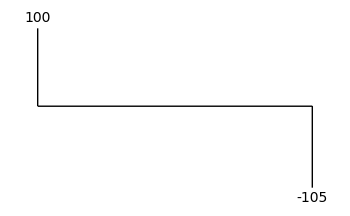

The additional $5.00 is, of course, the interest paid on the loan and represents an interest rate of 5%.

#### Multiple Payments Example

Another example would a case in which the borrower borrows $100 and pays back the loan with two payments, one at six months and the other at a year, of $51.88. The cash flow diagram in that case would be

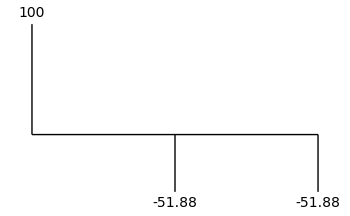

-Graphics-

The additional $1.88 + 1.88 = $3.76 represents the interest on the loan. Computing the interest rate here is slightly more complicated and will covered shortly.

### Loan: A Contract to Borrow Money Now and Repay It in the Future

A loan is a contract: The loaner gives the borrower a certain amount of money; the borrower agrees to repay this amount plus interest by making payments at specified points in time until the principal (the amount borrowed) plus interest is paid off.

#### A Simple Loan Example I — Multiple Payments

Frank loans $100 at 10% annual interest for 4 years to Andrea.

The principal, $100, is the amount borrowed.

The interest rate, 10%, represents the time value of money.

The term, 4 years, is the lifetime of the loan.

There will be additional conditions describing the details of the interest computations and the timing of payments from borrower to loaner.

In this case, the loan agreement stipulates that each year Andrea will pay the 10% interest on the $100 principal and at the end of the fourth year return the principal amount as well. The loan’s cash flow diagram from Andrea’s, the borrower’s, perspective is:

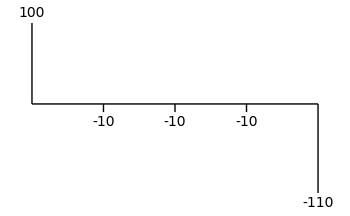

-Graphics-

#### A Simple Loan Example II — Single Payment

Consider the same loan above, except that Frank loans Andrea the $100 at 10% interest and receives a single lump-sum payment at the end of 4 years. Computing the interest due, and hence the payment, depends on certain conventions.

Simple Interest: In simple interest the interest is computed solely on the principal amount of the loan. In the loan example here the final payment would be computed by

100 × (1 + 4 × 0.10)=140

The cash flow diagram for this loan would be

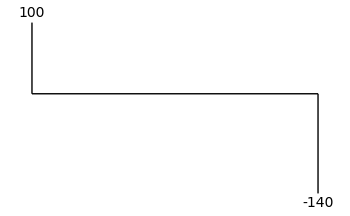

```mathematica
100(1+4 0.10)
```

140.

Thus, after 4 years Andrea pays Frank $140, the return of the $100 originally borrowed plus $40 interest.

Compound Interest: In compound interest, when interest accrues it is added to the balance owed. Future accruals of interest are applied to this new balance. If payments are made prior to the ending of the loan, then these are deducted from the balance. In our example, if interest is compounded semi-annually then every 6 months 5% interest, i.e., 10% / 2,  would be charged and accumulated in the balance owed. Over 4 years there are 8 such compounding events:

100 × (1+0.10/2)^(4 2)=100×(1.05)^8=147.75

The cash flow diagram for this loan would be

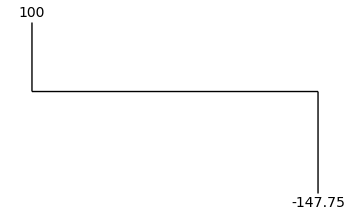

```mathematica
100(1+0.10/2)^(4 2)
```

147.746

Consider monthly compounding:

```mathematica
100(1+0.10/12)^(4 12)
```

148.935

Annually,

```mathematica
100(1+0.10)^4
```

146.41

In general, if we are charged interest on a present value of PV dollars at an interest of r compounded at k times per year for n years, then we receive a future value FV:

FV=PV × (1+r/k)^(n × k)

The weekly compounding at 10% over 4 years of $100.00 is

```mathematica
100(1+0.10/52)^(4 52)
```

149.125

## Compounding Frequency

Interest rates are usually quoted in terms of a nominal annual rate r and a compounding frequency k.

 Interest is accrued k-times per year at the rate of r / k.
 
 Alternately, instead of a compounding frequency k, we may specify a compounding interval q. Note that q=1/k.

### Quote Conventions for Interest Rates

r 	= nominal annual interest rate

k 	= compounding frequency

n	= term in years

### Accruing Discretely Compounded Interest

PV×(1+r/k)^(n × k)

PV×(1+r q)^(n  / q)

#### Example

$100 at 4% compounded at various frequencies for four years:

```mathematica
100(1+0.04/2)^(4 2)
```

117.166

```mathematica
100(1+0.04/12)^(4 12)
```

117.32

```mathematica
100(1+0.04/24)^(4 24)
```

117.335

```mathematica
100(1+0.04/52)^(4 52)
```

117.344

```mathematica
Limit[100(1+0.04/k)^(k 4),k->∞]
100 ⅇ^(4 0.04)
```

117.351

117.351

```mathematica
Clear[n]
```

```mathematica
Limit[(1+r/k)^(k n),k->∞]
```

ⅇ^(n r)

```mathematica
100 ⅇ^(-0.10 3)
```

74.0818

```mathematica
n=2
```

Set::wrsym: Symbol n is Protected.

2

```mathematica
n
```

n

```mathematica
Head[{1,2,3}]
```

List

```mathematica
Head[n]
```

Symbol

### Accruing Continuously Compounded Interest

As the compounding frequency increases interest accrues more rapidly, but it does approach a limit. Consider $1 at 10% compounded for 1 year at various frequencies:

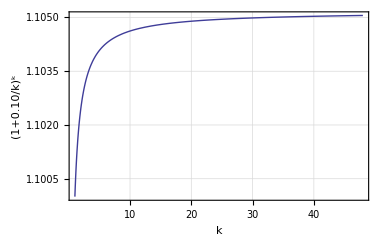

Consider investing F for n years at rate r at frequency k. Computing the limit as k → ∞ results in the exponential function:

lim_(k→∞) [PV (1+r/k)^(n × k)]=PV ⅇ^(n r)

```mathematica
Limit[P(1+r/k)^(n k),k->∞]
```

P ⅇ^(n r)

#### Example — Continuous Compounding

$1 at 10% compounded continuously for 1 year

```mathematica
ⅇ^0.10
```

1.10517

Overlaying this value on the plot above (red dashed line) we see it represents the asymptote to the compounding curve:

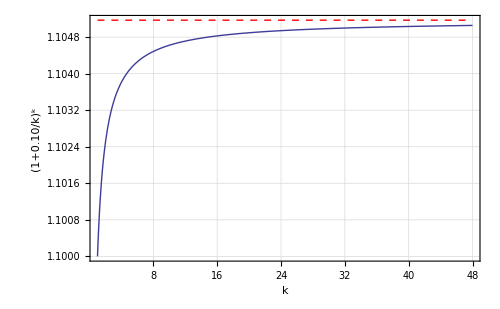

### ******Effective Annual Interest Rates

The effective annual interest rate, r_eff, of a nominal rate r compounded with frequency k is that rate that when compounded annually results in the same interest accrual:

1+r_eff=(1+r/k)^k   ⟹    r_eff=(1+r/k)^k-1

1+r_eff=ⅇ^r   ⟹    r_eff=ⅇ^r-1

#### Example

Consider a 2-year instrument with  r = 0.05 and  k = 12 the effective annual interest rate is 5.1%:

```mathematica
(1+0.05/12)^12-1
```

0.0511619

… and for k = 4 the effective annual interest rate is slightly lower:

```mathematica
(1+0.05/4)^4-1
```

0.0509453

Be careful not to confuse the term of the debt with the compounding frequency. The fact that we were dealing with a 2-year instrument is irrelevant here.

```mathematica
ⅇ^0.10-1
```

0.105171

## Calendar Conventions

In computing the length of time between two dates various calendar conventions are observed, often to simplify computation.

These are artifacts of the time before computers when these calculations were performed manually, but they remain standard in individual financial markets.

 For more information read: http://en.wikipedia.org/wiki/Day_count_convention

Consider the days between June 30, 2003 and December 12, 2004. Note the convention in Mathematica is to represent dates in {yyyy, mm, dd} form.

We' ll examine two different conventions in common use : Actual/Actual and 30/360. Students are warned that terminology varies from market to market and even from instrument to instrument within a market. Sometimes similar but slightly different conventions have the same name. Thus, context is important.

A large part of the software base for financial computations is dedicated to calendar computations covering computing the number of days between dates, the number of business (i.e., trading) days between dates, identification of holidays (which vary from country to country and market to market within country), calculating the standard expiration dates for various contracts, and many others related to time.

The function we need is DayCount[ ]:

```mathematica
?DayCount
```

### Actual/Actual

In the Actual/Actual convention each month and year is composed of the actual number of days.

```mathematica
DayCount[{2003,12,30},{2004,10,31}]
```

306

```mathematica
DayCount[{1990,11,25},{2019,8,28}]
```

10503

### 30/360

In the 30/360 convention months are assumed to have 30 days and a year is composed of 12 such months.

360 (y2 - y1) + 30 (m2 - m1 - 1) +( Min[d2, 30]+Max[30 - d1, 0] ])

```mathematica
360(2018-1990)+30(8-11-1)+(Min[31,8]+Max[30-25,0])
```

9973

### 30/365

In the 30/365 convention months are assumed to have 30 days and a year is composed of 12 such months.

## Present and Future Value

The concepts of present value and future value help us to think about how interest rates affect the price of many financial securities. 

They also allow us to re-express the price and associated cash flows of an asset in terms of the implied interest rate it pays, giving us a common basis for comparing two assets whose cash flows occur at different times.

Present and future value of cash flows are basic concepts used in the valuation and, therefore, comparison of cash flows

### Single Cash Flow Case

We’ll describe future and present value first in terms of a single cash flow.

#### Future Value

The future value, FV, is the total value realized from investing S at rate r compounded with frequency k for n years:

FV[S | r, k, n]=S × (1+r/k)^(n × k)

FV[S | r, ∞, n]=S × ⅇ^(n × r)

The FV of $1,000 at 10% compounded monthly for 5 years is:

```mathematica
1000(1+0.10/12)^(5 12)
```

1645.31

The FV of $1, 000 at 10 % compounded continuously for 5 years is :

```mathematica
1000 ⅇ^(5 0.10)
```

1648.72

#### Present Value

The present value is amount one would need to invest now to realize a given future cash flow. The present value, PV, of a cash flow F at interest rate r with compounding frequency k received n years in the future is:

PV[F | r, k, n]=F/(1+r/k)^(n × k)

PV[F | r, ∞, n]=F × ⅇ^(-n × r)

Alternately, it can be said that the PV value represents the discounted value of F. The value 1/(1+r/k)^(n×k) is called the discount factor.

The present value of $1,000 at 7.5% compounded quarterly received 5 years hence is:

```mathematica
1000/(1+0.075/4)^(5 4)
```

689.68

And note that the present and future value are consistent.

```mathematica
689.68(1+0.075/4)^(5 4)
```

1000.

### Multiple Cash Flows

The computation of the FV and PV for multiple cash flows are straightforward generalizations of the single cash flow cases. Let c_i denote the i^th cash-flow of 1+(n × k) cash flows generated over n years with compounding frequency k.

#### Future Value

The i^th cash flow experiences compound interest for (n×k)-i periods. We then sum the resulting FVs over all periods:

FV[{c_0,c_1,…,c_(n×k)} | r, k, n]=∑_(i=0)^(n×k) (c_i(1+r/k))^((n×k)-i)

#### Present Value

The i^th cash flow is discounted for i periods. We then sum the resulting PVs over all periods:

PV[{c_0,c_1,…,c_(n×k)} | r, k, n]=∑_(i=0)^(n×k) c_i/(1+r/k)^i

The terms (1+r/k)^-i are called discount factors. If we have a vector of cash flows c and vector of associated discount factors d, then working from the summation above, the PV is the inner product of the cash flows and their associated discount factors.

```mathematica
df={1,(1+0.1/2)^-1,(1+0.1/2)^-2,(1+0.1/2)^-3,(1+0.1/2)^-4}
```

{1,0.952381,0.907029,0.863838,0.822702}

```mathematica
cf={100,100,100,100,100}
```

{100,100,100,100,100}

```mathematica
cf.df
```

454.595

#### Internal Rate of Return (or Yield)

The internal rate of return, IRR, is that interest rate consistent with a PV of 0 for a given set of cash flows. Consider a case where the cash flows are received at each compounding interval, then

IRR[{c_0,c_1,…,c_(n×k)} | k, n]=solve_y [0=∑_(i=0)^(n×k) c_i/(1+y/k)^i]

Except in special cases, the IRR does not have a closed form solution and must be estimated numerically.

### Examples

#### PV of Stream of Constant Cash flows

PV[c received at 1/k to n in steps of 1/k | r, k, n]=c∑_(i=1)^(n×k) 1/(1+r/k)^i

```mathematica
1000.∑_(i=1)^(10 12) 1/(1+0.08/12)^i
```

82421.5

```mathematica
FullSimplify[∑_(i=1)^(n k) 1/(1+r/k)^i]
```

(k-k ((k+r)/k)^(-k n))/r

```mathematica
1000.(12(1-((12+0.08)/12)^(-12 10)))/0.08
```

82421.5

```mathematica
Timing[1000.∑_(i=1)^(10 12) 1/(1+0.08/12)^i]
```

{0.000219,82421.5}

```mathematica
Timing[1000.(12(1-((12+0.08)/12)^(-12 10)))/0.08]
```

{0.000017,82421.5}

#### PV of Periodic Cash Flows with Continuous Compounding

Consider a series of monthly payments of $200 for 101/2 years at 4% compounded continuously. Note that the i^th payment occurs at time i / k:

PV=200∑_(i=1)^(10.5×12) ⅇ^(-r i/k)

#### IRR Example

Consider a case in which an investor buys a bond for $950 that pays a semi-annual coupon of $50 for 10 years. For the final payment the investor receives a settlement of $1,000 in addition to the last coupon payment.

We’ll use a brute force approach here but will show later how it can be considerably simplified.

We will use two Mathematica functions is this computation, the iterator Table[ ]  and the selector Which[ ]. In addition, note that given two vectors x and y, their inner product is denoted by x.y:

```mathematica
?Table
```

```mathematica
Table[i^2,{i,0,10,2}]
```

{0,4,16,36,64,100}

```mathematica
?Which
```

```mathematica
vnCashflows=Table[Which[i==0,-950,i==2 10,1050,True,50],{i,0,2 10}]
```

{-950,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,50,1050}

The cash flow diagram for this problem from the bond purchaser’s perspective is:

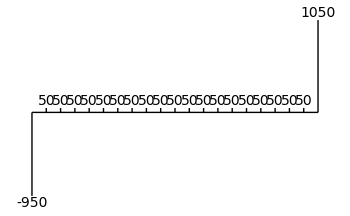

-Graphics-

The associated discount factors for each period are:

```mathematica
vnDiscountFactors=Table[(1+y/2)^-i,{i,0,2 10}]
```

{1,1/(1+y/2),1/(1+y/2)^2,1/(1+y/2)^3,1/(1+y/2)^4,1/(1+y/2)^5,1/(1+y/2)^6,1/(1+y/2)^7,1/(1+y/2)^8,1/(1+y/2)^9,1/(1+y/2)^10,1/(1+y/2)^11,1/(1+y/2)^12,1/(1+y/2)^13,1/(1+y/2)^14,1/(1+y/2)^15,1/(1+y/2)^16,1/(1+y/2)^17,1/(1+y/2)^18,1/(1+y/2)^19,1/(1+y/2)^20}

```mathematica
vnCashflows.vnDiscountFactors
```

-950+1050/(1+y/2)^20+50/(1+y/2)^19+50/(1+y/2)^18+50/(1+y/2)^17+50/(1+y/2)^16+50/(1+y/2)^15+50/(1+y/2)^14+50/(1+y/2)^13+50/(1+y/2)^12+50/(1+y/2)^11+50/(1+y/2)^10+50/(1+y/2)^9+50/(1+y/2)^8+50/(1+y/2)^7+50/(1+y/2)^6+50/(1+y/2)^5+50/(1+y/2)^4+50/(1+y/2)^3+50/(1+y/2)^2+50/(1+y/2)

There are several approaches in Mathematica for solving this problem. One of the most straightforward is FindRoot[ ]:

```mathematica
?FindRoot
```

We need a starting point for FindRoot[ ]. The bond pays $100 per year in coupon and the price is 950, so our initial estimate will be 100/950:

```mathematica
FindRoot[vnCashflows.vnDiscountFactors==0,{y,100./950.}]
```

{y→0.108309}

The IRR for this cash-flow problem is 10.83%.

There is usually more way than one to accomplish something in Mathematica. Consider an alternate set up:

```mathematica
100./950.
```

0.105263

```mathematica
FindRoot[0==-950+50∑_(i=1)^(10 2) (1+y/2)^-i+1000(1+y/2)^(-10×2),{y,0.05}]
```

{y→0.108309}

### Mathematica Tools for PV and FV Calculations

Mathematica contains a number of objects that work together to simplify the computation of time value of money computations. The main difference in form from the computations above is that they use the compounding interval q instead of the compounding frequency k.

```mathematica
?TimeValue
```

```mathematica
?EffectiveInterest
```

```mathematica
?Cashflow
```

```mathematica
?Annuity
```

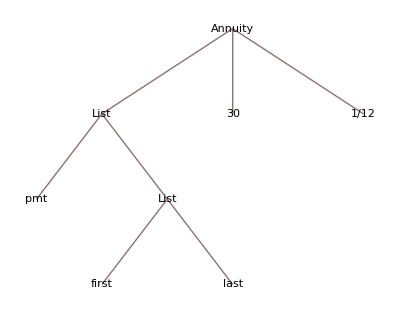

```mathematica
TreeForm[Annuity[{pmt,{first,last}},30,1/12]]
```

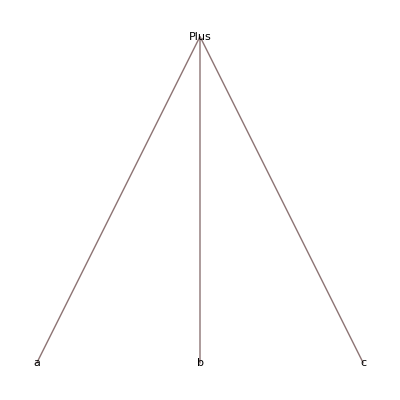

```mathematica
TreeForm[a+b+c]
```

```mathematica
Plus[a,b,c]
```

a+b+c

#### Simple FV

FV of $1000 at an interest rate of 5% compounded annually for 3 years:

```mathematica
TimeValue[1000,0.05,3]
```

1157.63

```mathematica
1000(1+0.05)^3
```

1157.63

#### FV Quarterly Frequency

FV of $1000 at an interest rate of 5% compounded quarterly for 10 years:

```mathematica
TimeValue[1000,EffectiveInterest[.05,1/4],10]
```

1643.62

```mathematica
1000(1+0.05/4)^(10 4)
```

1643.62

#### PV Semi-Annual Frequency

PV of $1000 at 5% interest compounded semi-annually received in 10 years:

```mathematica
TimeValue[1000,EffectiveInterest[0.05,1/2],-10]
```

610.271

```mathematica
1000.(1+0.05/2)^(-10  2)
```

610.271

```mathematica
1000./(1+0.05/2)^(10  2)
```

610.271

Note that TimeValue[ ]  works with symbolic arguments:

```mathematica
TimeValue[c,r,-n]
```

c (1+r)^-n

```mathematica
TimeValue[c,EffectiveInterest[r,1/k],-n]
```

c ((1+r/k)^k)^-n

```mathematica
x
```

x

```mathematica
D[x^5,x]
```

5 x^4

```mathematica
x=9
```

Set::wrsym: Symbol x is Protected.

9

```mathematica
x=5
```

Set::wrsym: Symbol x is Protected.

5

```mathematica
3x
```

3 x

#### PV of a Series of Fixed Payments

PV at 6% of a 4-year annuity with monthly payments of $100:

```mathematica
?Annuity
```

```mathematica
TimeValue[Annuity[100,4,1/12],EffectiveInterest[0.06,1/12],0]
```

4258.03

```mathematica
?Cashflow
```

```mathematica
Table[100,{3}]
```

{100,100,100}

```mathematica
Prepend[Table[100,{4 12}],0.]
```

{0.,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100}

```mathematica
Cashflow[Prepend[Table[100,{4 12}],0.],1/12]
```

Cashflow[{0.,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100},1/12]

```mathematica
TimeValue[Cashflow[Prepend[Table[100,{4 12}],0.],1/12],EffectiveInterest[0.06,1/12],0]
```

4258.03

```mathematica
100.∑_(i=1)^(4 12) (1+0.06/12)^-i
```

4258.03

#### FV with Date Specified

Future value in three years' time of $1000 invested on January 1, 2010 at 7.5%:

```mathematica
TimeValue[1000,.075,{{2013,1,1},{2010,1,1}}]
```

1242.3

```mathematica
TimeValue[c,r,{{2013,1,1},{2010,1,1}}]
```

c (1+r)^3

Consider an ending date of {2013, 02, 01}:

```mathematica
TimeValue[c,r,{{2013,2,1},{2010,1,1}}]
```

c (1+r)^3.08493

How is the exponent 3.08493 calculated? The default is to use the Actual/Actual calendar convention. The time from {2010, 1, 1} to {2013, 1, 1} is 3 years. The remaining period from {2013, 1, 1} to {2013, 2, 1} is the number of days between these dates divided by the number of days in that year. Here is a direct calculation of the exponent using DaysBetween[ ] to compute the number of days in the final year and the total number of days in that year:

```mathematica
3.+DayCount[{2013,1,1},{2013,2,1}]/DayCount[{2012,12,31},{2013,12,31}]
```

3.08493

TimeValue[ ] supports a number of other calendar conventions. Read its entry in the Documentation Center for the details.

#### Solve for the IRR

Solve for the IRR of a series of $450 monthly payments made over 15 years that are valued at $62,500:

```mathematica
FindRoot[ TimeValue[Annuity[450,15,1/12],EffectiveInterest[r,1/12],0]==62500,{r,.03}]
```

{r→0.0360399}

```mathematica
1+r/.{r->0.03603986823928565}
```

1.03604

```mathematica
FindRoot[450.∑_(i=1)^(15 12) 1/(1+r/12)^i==62500,{r,0.03}]
```

{r→0.0360399}

#### PV with Continuous Compounding

Note that lim_(k→∞) [1/k]=0; hence, we specify continuous compounding with a wavelength of q = 0:

```mathematica
TimeValue[c,EffectiveInterest[r,0],-n]
```

c (ⅇ^r)^-n

```mathematica
c (ⅇ^r)^-n/.{c->100,r->0.05,n->10}
```

60.6531

```mathematica
c=100
```

100

```mathematica
TimeValue[c,EffectiveInterest[r,0],-n]
```

100 (ⅇ^r)^-n

```mathematica
r=0.05
n=20
```

0.05

20

```mathematica
TimeValue[c,EffectiveInterest[r,0],-n]
```

36.7879

## Fixed Income Securities

Fixed income securities are financial instruments that represent the seller's promise to pay a "fixed" set of payments to the buyer (http://en.wikipedia.org/wiki/Fixed_income_securities). 

The term "fixed" must be taken in context; the interest rate upon which the payments are based may vary with market conditions.

### Markets for Cash

#### Savings Deposits

The simplest is the demand deposit, in which the cash must be returned upon the demand of the owner. The other alternates, time deposit accounts and certificates of deposit, require the funds to remain for a fixed period of time.

#### Money Market Instruments

These are short-term borrowing by corporations or banks. The term commercial paper is used to describe unsecured loans of this type.

#### U. S. Government Securities

These are a form of what is called sovereign debt.

U.S. Treasury Bills: Issued in denominations of $10,000 or more and fixed maturities of 13, 26 and 52 weeks. They are sold at discount. Thus, for example, a $10,000 13-week bill at a 5% yield would be sold for 10,000 / (1 + 0.05 / 4) = $9,876.54.

U.S Treasury Notes: Have maturities of 1 to 10 years and are sold in denominations of $1,000 or more. The holder receives a fixed coupon payment every six months until the end of the term at which time the holder receives the final coupon payment and the return of the face or principal amount of the note.

U.S. Treasury Bonds: Have maturities of 10-years or more. They make semi-annual coupon payments like Treasury notes, but are callable, i.e.. at scheduled coupon payment dates the Treasury can call the bond, redeeming it by returning the face amount at that time.

U.S. Treasury Strips: Are Treasuries whose coupon and principal payments have been stripped into separate instruments. For example, a $1,000, 10-year bond would be stripped into its 20 coupon payments plus its principal. These individual instruments, each of which are a single fixed payment at fixed point in time, are called zero coupon bonds.

#### Other Bonds

Municipal Bonds: Are issued by government (Federal, state and local) to help fund their operations or capital projects. Some bonds are revenue bonds, which are guaranteed by the revenue from a specific project such as a bridge or highway, and general obligation bonds, which are guaranteed by the taxing authority of the government agency. The interest income is exempt from Federal taxes and from state and local taxes in the issuing state. This allows government agencies to pay a lower rate than other borrowers.

Corporate Bonds: Are issued by corporations to raise capital for their operations and capital projects. Depending upon the borrower, such bonds carry varying risks of default, i.e., failure of the issuer to able to repay the debt. The higher the risk of default, the higher the interest rate that must be paid in order to compensate lenders to take that risk on.

#### Special Conditions

Sinking Funds are often set up in which the borrower is required to set aside cash in preparation for paying the bond.

Callable bonds can be redeemed at the issuer's discretion at specified points over the term of the debt.

Subordination of debt occurs when other more senior debt must be paid off first. More senior debt obviously carries less risk than less senior debt.

Secured bonds are debt whose is secured by specific assets. Holders of secured bonds can seek to recover the asset if the issuer defaults.

#### Mortgages

A mortgage is a loan secured by some asset. The terms are usually the reverse of that of a bond. The holder receives a fixed amount of cash from the issuer and usually agrees to pay a series of equal payments at regular intervals over a specified term. Most homes are purchased with the help of a mortgage.

#### Annuities

In an annuity a contract is entered into in which the holder or annuitant is paid money according to a set schedule over some period of time. There are several types of annuities. Sometimes the payments are fixed and sometimes the payments are based on an index or market rate.

### Valuation

#### Perpetual Annuity

A perpetual annuity, sometimes called a consol, is one in which the holder gives the issuer an amount S and the issuer agrees to pay the holder a coupon c at regular intervals in perpetuity.

S=∑_(i=1)^∞ c/(1+y/k)^i=k c/y=c/(y/k)

For example, the value of a consol with a semi-annual coupon of $100 where the annual rate is 5%  is $4, 000.

```mathematica
2 100/0.05
```

4000.

```mathematica
100/(0.05/2)
```

4000.

#### Finite Life Streams

Consider a variation on the above in which the payment ends after n periods.

P=∑_(i=1)^n c/(1+r)^i=c/r(1-1/(1+r)^n)

P=∑_(i=1)^(n×k) c/(1+r/k)^i=c/(r/k)(1-1/(1+r/k)^(n×k))

The derivation of this formula is straightforward. We can consider the finite stream over n-years as represented by one perpetual annuity less another perpetual annuity that commences n-years hence. This difference produces the identical cash-flows, and, therefore, its PV is the same as that of the finite stream. The PV of the first peputual annuity is c /r and the PV of the second perpetual annuity is (c/r)/(1+r)^n. The result above follows directly.

We can also use Mathematica to solve for the closed-form solution:

```mathematica
ClearAll[r,c,n,k]
```

```mathematica
FullSimplify[∑_(i=1)^(n k) c/(1+Subscript[r, period]/k)^i]
```

(c k (1-((k+r_period)/k)^(-k n)))/r_period

For example, the value of an annuity with a semi - annual coupon of $100 where the annual rate is 5%  and the term is 10 years. This is a finite stream with r = 2.5% and n = 20:

```mathematica
100/0.025(1-1/(1+0.025)^20)
```

1558.92

Alternately, for n years,  frequency k and annual rate r, the number of periods is now k × n and the single period rate is r/k. Thus,

P=∑_(i=1)^(n × k) c/(1+r/k)^i=k c/r(1-1/(1+r/k)^(n × k))

Using the same example, the value of an annuity with a semi - annual coupon of $100 where the annual rate is 5%  and the term is 10 years is

```mathematica
100∑_(i=1)^(10 2) (1+0.05/2)^-i
```

1558.92

Or using the closed-form solution:

```mathematica
2 100/0.05(1-1/(1+0.05/2)^(2 10))
```

1558.92

The usual convention in most markets is to describe the term in years, the rate as a nominal annual rate, and the compounding frequency in frequency per year.

## Mortgages

Mortgages are loans secured by real property. In other words the bank or financial institution has a claim on the property in the event the mortgage is not repaid. Mortgage loans vary considerably in their terms.

Fixed-rate, fixed-term loans are the most common. Some other forms will also be covered. 

Most purchases of real property are accomplished by placing a down payment to cover a portion of the price and then financing a significant portion of the residual through a mortgage.

Read http://en.wikipedia.org/wiki/Mortgage for more information.

### Fixed-Rate, Fixed-Term Mortgages

In a fixed-rate, fixed-term mortgage the borrower receives the initial loan balance B from the lender and agrees to pay the lender a stream of fixed payments p at regular intervals k-times per year until the end of the term of the loan. These payments are typically monthly and are computed based on a nominal annual rate r.

ment stream at the mortgage’s interest rate r and payment frequency k matches the initial loan balance B:

solve_p [B=p∑_(i=1)^(n × k) 1/(1+r/k)^i]

solve_p [B==TimeValue[Annuity[p,n,1/k], EffectiveInterest[r,1/k],0]]

Here is the cash-flow from the perspective of the borrower who receives the balance B of the mortgage at the beginning and makes k (almost always monthly) payments p over the term of the loan:

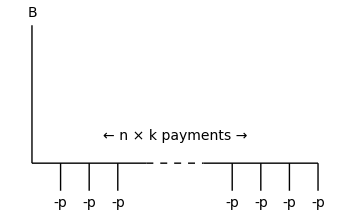

#### Example — Computing the Monthly Payment

Consider a monthly mortgage for $95,000 borrowed for 15 years at rate of 4.5%.:

```mathematica
?FindRoot
```

```mathematica
FindRoot[95000==TimeValue[Annuity[p,15,1/12],EffectiveInterest[0.045,1/12],0],{p,95000 0.045/12}]
```

{p→726.744}

The required payment is $726.744 per month.

#### Example — Computing an Affordable Mortgage Amount

A home buyer estimates that she can afford a mortgage of $575 per month. If current 30-year mortgage rates are 3.75%, then what is the maximum mortgage that she can afford?

```mathematica
TimeValue[Annuity[575,30,1/12],EffectiveInterest[0.0375,1/12],0]
```

124159.

The maximum mortgage is $124,159.

### Amortization of a Fixed-Rate, Fixed-Term Mortgage

At each payment date a portion of the payment goes to paying the interest accrued since the last payment. The remainder is used to pay down the remaining balance owed on the loan.

Amortization here refers to the calculation of interest and principal paid at each payment of a loan. One approach is to compute it recursively. Let

B_i	= the balance at the end of the i^th payment period

I_i	= the interest accrued during the i^th payment period

P_i	= the principal paid during the i^th payment period

The recursion is initialized with

B_0=B

Then for i from 1 to n × k

The interest accrued is the amount owed at the end of the prior period times the periodic rate:

I_i=r/k B_(i-1)

The principal paid is that portion of the periodic payment that is not required to cover the accrued interest:

P_i=p-I_i

The new balance is the prior balance less the principal paid:

B_i=B_(i-1)-P_i

#### Example—Recursive Amortization Calculation

The amortization calculation is illustrated by an example. For simplicity we will assume that the mortgage payments occur semi-annually:

```mathematica
nLoanAmount=100000;
nAnnualRate=0.05;
iTerm=15;
iFrequency=2;
```

The semi-annual mortgage payment is:

```mathematica
FindRoot[nLoanAmount==TimeValue[Annuity[p,iTerm,1/iFrequency],EffectiveInterest[nAnnualRate,1/iFrequency],0],{p,nLoanAmount( nAnnualRate/iFrequency)}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{p→4777.76}

```mathematica
nPayment=p/.FindRoot[nLoanAmount==TimeValue[Annuity[p,iTerm,1/iFrequency],EffectiveInterest[nAnnualRate,1/iFrequency],0],{p,nLoanAmount( nAnnualRate/iFrequency)}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

4777.76

```mathematica
nPayment
```

4777.76

Given the warning, it’s wise to double check the result by plugging the payment back in to see if we recover the proper loan amount.

```mathematica
TimeValue[Annuity[nPayment,iTerm,1/iFrequency],EffectiveInterest[nAnnualRate,1/iFrequency],0]
```

100000.

NestList[ ] is an iterator that applies a function recursively

```mathematica
?NestList
```

```mathematica
NestList[f,x,3]
```

{x,f[x],f[f[x]],f[f[f[x]]]}

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
NestList[Sin,1.1,1000];
```

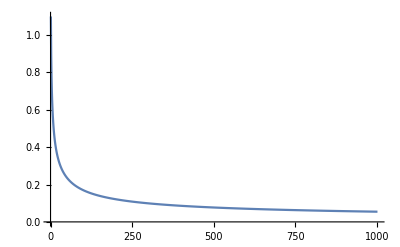

```mathematica
ListLinePlot[%,PlotRange->All]
```

We next code a function to execute one iteration of the above recursion. The function takes the (i-1)^th period’s amortization data and mortgage specification, and returns the i^th period’s amortization data:

{t_i, I_i,P_i,B_i}=xAmortizationRecursion[ {t_(i-1), I_(i-1),P_(i-1),B_(i-1)}, {p, r, n, k}]

```mathematica
xAmortizationRecursion[
{nTime_,nInterestPaid_,nPrincipalPaid_,nBalance_},
{nPayment_,nAnnualRate_,iTerm_,iFrequency_}
]:=Module[
{thisTime,thisBal, thisInt,thisPrin},
thisTime=nTime+ 1./iFrequency;
thisInt=nBalance nAnnualRate/iFrequency;
thisPrin=nPayment-thisInt;
thisBal=nBalance-thisPrin;
{thisTime,thisInt,thisPrin,thisBal}
];
```

```mathematica
3#+2&[4]
```

14

Then apply NestList[ ] to recursively compute the amortization schedule. The Mathematica statement

xAmortizationRecursion[#,{nPayment,nAnnualRate,iTerm,iFrequency}]&

is a function that places its argument into the slot denoted by “#” and then evaluates the expression. We do this so that the recursion performed in NestList[ ] just has to pass the prior {t_i, I_i,P_i,B_i} state given the fixed loan definition {p,r,n,k}.

```mathematica
mnAmortization=NestList[
xAmortizationRecursion[#,{nPayment,nAnnualRate,iTerm,iFrequency}]&,
{0,0,0,nLoanAmount},
iTerm iFrequency
]
```

{{0,0,0,100000},{0.5,2500.,2277.76,97722.2},{1.,2443.06,2334.71,95387.5},{1.5,2384.69,2393.08,92994.5},{2.,2324.86,2452.9,90541.5},{2.5,2263.54,2514.23,88027.3},{3.,2200.68,2577.08,85450.2},{3.5,2136.26,2641.51,82808.7},{4.,2070.22,2707.55,80101.2},{4.5,2002.53,2775.23,77326.},{5.,1933.15,2844.62,74481.3},{5.5,1862.03,2915.73,71565.6},{6.,1789.14,2988.62,68577.},{6.5,1714.42,3063.34,65513.6},{7.,1637.84,3139.92,62373.7},{7.5,1559.34,3218.42,59155.3},{8.,1478.88,3298.88,55856.4},{8.5,1396.41,3381.35,52475.1},{9.,1311.88,3465.89,49009.2},{9.5,1225.23,3552.53,45456.6},{10.,1136.42,3641.35,41815.3},{10.5,1045.38,3732.38,38082.9},{11.,952.073,3825.69,34257.2},{11.5,856.431,3921.33,30335.9},{12.,758.397,4019.37,26316.5},{12.5,657.913,4119.85,22196.7},{13.,554.917,4222.85,17973.8},{13.5,449.346,4328.42,13645.4},{14.,341.135,4436.63,9208.78},{14.5,230.219,4547.54,4661.23},{15.,116.531,4661.23,-2.30466×10^-9}}

The Chop[ ] function is used to clean up values that are "near" zero that may result from inconsequential rounding.

```mathematica
?Chop
```

TableForm[ ] is used to produce formatted tabular results.

```mathematica
?TableForm
```

The amortization schedule for the loan can now be produced:

```mathematica
TableForm[
Chop[mnAmortization,10^-4],
TableHeadings->{Range[0,iTerm iFrequency],{"t","I_i","P_i","B_i"}}
]
```

| t | I_i | P_i | B_i
0 | 0 | 0 | 0 | 100000
1 | 0.5 | 2500. | 2277.76 | 97722.2
2 | 1. | 2443.06 | 2334.71 | 95387.5
3 | 1.5 | 2384.69 | 2393.08 | 92994.5
4 | 2. | 2324.86 | 2452.9 | 90541.5
5 | 2.5 | 2263.54 | 2514.23 | 88027.3
6 | 3. | 2200.68 | 2577.08 | 85450.2
7 | 3.5 | 2136.26 | 2641.51 | 82808.7
8 | 4. | 2070.22 | 2707.55 | 80101.2
9 | 4.5 | 2002.53 | 2775.23 | 77326.
10 | 5. | 1933.15 | 2844.62 | 74481.3
11 | 5.5 | 1862.03 | 2915.73 | 71565.6
12 | 6. | 1789.14 | 2988.62 | 68577.
13 | 6.5 | 1714.42 | 3063.34 | 65513.6
14 | 7. | 1637.84 | 3139.92 | 62373.7
15 | 7.5 | 1559.34 | 3218.42 | 59155.3
16 | 8. | 1478.88 | 3298.88 | 55856.4
17 | 8.5 | 1396.41 | 3381.35 | 52475.1
18 | 9. | 1311.88 | 3465.89 | 49009.2
19 | 9.5 | 1225.23 | 3552.53 | 45456.6
20 | 10. | 1136.42 | 3641.35 | 41815.3
21 | 10.5 | 1045.38 | 3732.38 | 38082.9
22 | 11. | 952.073 | 3825.69 | 34257.2
23 | 11.5 | 856.431 | 3921.33 | 30335.9
24 | 12. | 758.397 | 4019.37 | 26316.5
25 | 12.5 | 657.913 | 4119.85 | 22196.7
26 | 13. | 554.917 | 4222.85 | 17973.8
27 | 13.5 | 449.346 | 4328.42 | 13645.4
28 | 14. | 341.135 | 4436.63 | 9208.78
29 | 14.5 | 230.219 | 4547.54 | 4661.23
30 | 15. | 116.531 | 4661.23 | 0

We do not need to iteratively work through an amortization schedule if we are interested in computing the balance due at a particular point in time. If there are n_remaining years left on the loan, then the residual balance is the PV of the remaining payments. For example, if we have paid the the loan for 10 years, then the remaining balance is the PV of the remaining 5 years of payments:

```mathematica
TimeValue[Annuity[nPayment,5,1/iFrequency],EffectiveInterest[nAnnualRate,1/iFrequency],0]
```

41815.3

and this matches the above amortization schedule’s balance for payment 20.

Amortization is used to determine tax detectability (interest is deductible but principal is not) and the current balance in the event the borrower wishes to pre-pay.

If we plot the the interest and principal paid at each payment, then we see that in as time goes on the interest owed each period decreases as more and more of the balance of the mortgage is paid:

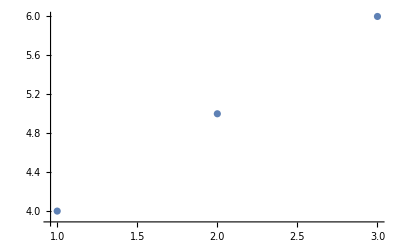

```mathematica
ListPlot[{{1,2,3},{4,5,6}}ᵀ]
```

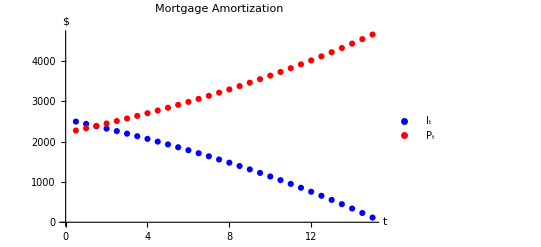

```mathematica
ListPlot[
{{Rest[mnAmortization⟦All,1⟧],Rest[mnAmortization⟦All,2⟧]}ᵀ,{Rest[mnAmortization⟦All,1⟧],Rest[mnAmortization⟦All,3⟧]}ᵀ},
PlotStyle->{{Thick,Blue},{Thick,Red}},
PlotLegends->{"I_t","P_t"},
AxesLabel->{"t","$"},
PlotLabel->Style["Mortgage Amortization",FontSize->14]
]
```

The remaining balance at each point in time is:

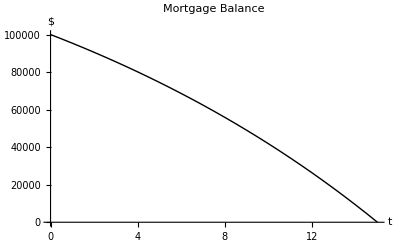

```mathematica
ListLinePlot[
Transpose[{mnAmortization⟦All,1⟧,mnAmortization⟦All,4⟧}],
AxesLabel->{"t","$"},
PlotLabel->Style["Mortgage Balance",FontSize->14],
PlotStyle->{Black,Thick}
]
```

The total interest paid and principal are:

```mathematica
Total[mnAmortization⟦All,2⟧]
```

43332.9

```mathematica
Total[mnAmortization⟦All,2⟧]
Total[mnAmortization⟦All,3⟧]
```

43332.9

100000.

```mathematica
nPayment iTerm iFrequency
```

143333.

### Interest-Only Mortgage

In an interest-only mortgage, the borrower pays only the interest due on the loan each month. At the end of the term the full amount of the principal must be repaid as a balloon payment. Generally, the borrower operates under the assumption that the value of the property will appreciate over the term and, hence, he or she will be able to sell the property for a profit or use the higher value to renegotiate a new mortgage without difficulty.

The monthly payment is the monthly interest on the principal:

p=B r/k

The final payment is a balloon that is the sum of the month’s interest and the principal. The cash-flow diagram from the borrower’s perspective is:

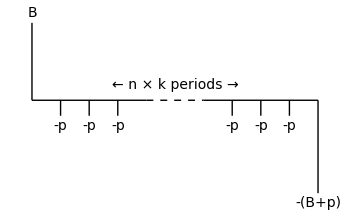

### Commercial Mortgages

In some instances, especially when commercial property is involved, the mortgage payment is computed based on a term n_amort but the actual term of the loan is n, where n_amort>n. At the end of n years the final payment is a balloon that consists of the month’s payment plus the unpaid portion of the principal. These mortgages are attractive to the bank because it can offer a competitive fixed-rate without committing itself to that rate over a long period of time. The borrower normally expects to remortgage the property at n at the mortgage rate available in the market at that time.

The required payment is:

p=solve_p [B==TimeValue[Annuity[p,n_amort,1/k], EffectiveInterest[r,1/k],0]]

The residual unpaid balance R is the PV of the “remaining” cash-flows, i.e., of a mortgage with term n_amort-n:

R==TimeValue[Annuity[p,n_amort-n,1/k], EffectiveInterest[r,1/k],0]

The cash-flow diagram from the borrowers perspective is:

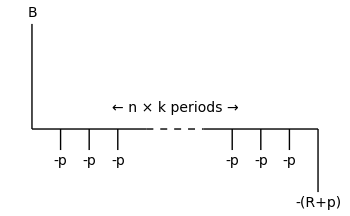

#### Example

The XYZ Corporation wishes to buy a new corporate headquarters. It takes out a $5,000,000 mortgage with a 5-year term with payments set at a rate of 7.5% with a 15-year amortization.

The monthly payment is computed based on a 15-year mortgage:

```mathematica
nPMT=p/.FindRoot[5 10^6==TimeValue[Annuity[p,15,1/12],EffectiveInterest[0.075,1/12],0],{p,5 10^6 0.075/12}]
```

46350.6

The residual balance owed and final balloon payment is:

```mathematica
nRESID=TimeValue[Annuity[nPMT,10,1/12],EffectiveInterest[0.075,1/12],0]
```

3.9048×10^6

```mathematica
nRESID+nPMT
```

3.95115×10^6

Thus, the monthly payments are $46,350.60 with a final balloon at the end of 5 years of $3,951,150.

As you might expect, if the market price of the real estate has not gone up but decreased over the term of the mortgage, then the borrower may have severe difficulty remortgaging the property to cover the balloon. In the case above the residual balance is 3.9/5=0.78. Thus, if property values have fallen more than 22% over the intervening period, this could cause serious problems for the building’s owner if it did not have enough capital to place an additional amount down to reduce the new mortgage balance.

### More Mortgages

In recent years a number of complex schemes have emerged: mortgages whose rates are not fixed but float with the market, mortgages with fixed-rates for a certain period of time which then reset to another rate depending upon some algorithm, negative amortization mortgages where the monthly payment is insufficient to cover the interest and the balance actually grows with time. Many consumers have gotten into financial trouble because they have not understood the mortgage contracts they signed and were surprised when the monthly payments were suddenly adjusted upwards or when they tried to sell their house and found that the amount they owed was greater than the amount they originally borrowed. The Wikipedia entry cited above discusses these in more detail.

## Bonds

From Wikipedia http://en.wikipedia.org/wiki/Bond_(finance):

A bond is a debt security, a contract to repay borrowed money plus interest. The borrower is called the issuer of the bond. The lender is called the holder of the bond. Short-term debt instruments such as certificates of deposit, CDs, are not considered bonds.
	
Bonds are used commercially to secure external capital without diluting the ownership of the business and are usually issued for purposes of long-term investment. 

Governments and governmental agencies also issue bonds, which may be used to fund either long-term projects such as schools or bridges or to fund shortfalls in current expenditures.

	Bonds typically have a defined term, or maturity and a fixed schedule of interest payments, called the coupons. At the end of the term the face amount of the bond is repaid. An exception is a consol bond, which is an agreement to pay the coupon in perpetuity.

Price: the amount the bond holder (the lender) agrees to pay the issuer (the borrower) to own the bond at origination or the price a purchaser has to pay in the secondary market to own the bond.

Par or face value: the amount the coupon payment is based and, usually, the amount the bond issuer agrees to pay the bond holder at redemption.

Term: the time over which the obligations represented by the bond exist.

Rate of interest: the interest, usually expressed as an annual number, paid on the face amount of the bond.

Payment frequency: the number of times each year the bond pays.

Coupon: the periodic payment on the bond; usually an interest payment based on the face amount, interest rate and payment frequency.

Yield: is the IRR of the bond at the market price. Yield, rather than price, is the primary measure used to value and compare bonds in the market.

Premium or Discount: A bond that is sold at origination at a price higher that its par value is said to sell at a premium. If less, at a discount.

Rating: is a measure of how likely the bond is to default; ratings are usually standardized (see, for example, http://en.wikipedia.org/wiki/Bond_rating). The lower the rating, the higher the interest rate that must be paid to compensate the lender for the additional risk.

### Simple Bond

In what follows we will assume that a standard bond priced at S with face value F, interest rate r, term n and frequency k. The coupon c is calculated from the face value, annual rate and frequency:

c=F r/k

c=F r q      (where q = 1/k)

In most cases a bond works by

The buyer (the lender) pays the market price to the seller (the issuer in a primary sale or the current holder in a secondary sale).

The borrower (the original issuer) pays the holder a periodic and (usually) fixed coupon payment, (usually) semi-annually.

At the end of the term the borrower pays the holder the final coupon payment and the face amount of the bond.

The cash-flow diagram from the issuer’s (i.e., the borrower’s) perspective at origination for a typical bond looks like:

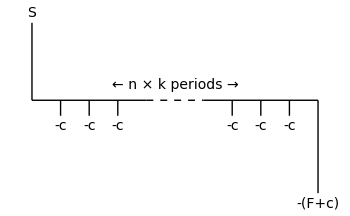

### Zero Coupon Bond

A zero coupon bond is a bond purchased at origination at a discount which makes a single payment of its face amount at the end of its term. The cash-flow diagram from the borrower’s perspective is:

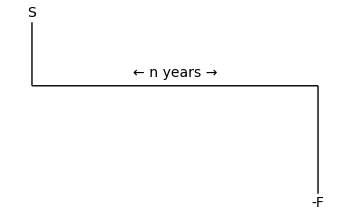

### Consol

A consol is a bond that pays its coupon into perpetuity. Consols are normally issued by sovereign governments. The periodic coupon payment is computed in the usual manner. The cash-flow diagram of a consol from the borrower’s perspective is:

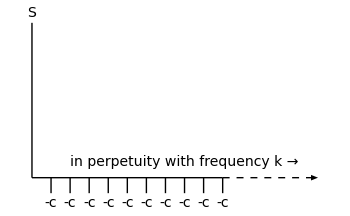

### Bond Yield

The yield of a bond is its IRR. The value of a bond is often quoted in terms of its yield rather than its price. This is to facilitate the comparison of different bonds that have different underlying structures. The price of the bond is the PV of the finite stream of coupon payments plus the PV of the final payment of the face amount discounted at the yield of the bond:

S=∑_(i=1)^(n × k) c/(1+y/k)^i+F/(1+y/k)^(n × k)=k c/y(1-1/(1+y/k)^(n × k))+F/(1+y/k)^(n × k)

The yield represents the return that the market demands for an instrument of this type. The price S is the PV of the cash-flows at the market return. Often we have the price of the bond and must solve for the yield:

solve_y[S=k c/y(1-1/(1+y/k)^(n × k))+F/(1+y/k)^(n × k)]

When a bond is sold such that

y = r :	The bond is sold at par and its IRR matches the coupon rate. This implies that the coupon rate the bond matches the market’s rate, the yield, used to price this instrument. The PV of the cash-flows matches the face amount.

y < r :	The bond is sold at a premium and the coupon rate of the bond is greater than the market yield. The PV of the cash-flows is higher than the face amount.

y > r :	The bond is sold at a discount and the coupon rate of the bond is less than the market yield. The PV of the cash-flows is less than the face amount.

#### Bond at Discount Example

Consider a bond with the following description:

```mathematica
nPrice=9900;
nFace=10000;
nCouponRate=0.05;
iTerm=10;
iFrequency=2;
```

The semi-annual coupon is therefore:

```mathematica
nCoupon=nFace(nCouponRate/iFrequency)
```

250.

To kick off the search we need an initial estimate of the yield. A reasonable value will be the amount of coupon paid over the year divided by the price of the bond. This results in a starting estimate of 5.05%.

```mathematica
nInitialRateGuess=(nCoupon iFrequency)/nPrice
```

0.0505051

The solution can now be calculated numerically using FindRoot[ ]:

```mathematica
FindRoot[
nPrice==nFace/(1+y/iFrequency)^(iFrequency iTerm)+iFrequency nCoupon/y(1-1/(1+y/iFrequency)^(iFrequency iTerm)),
{y,nInitialRateGuess}
]
```

{y→0.0512908}

The yield of the bond is 5.13%.

#### Bond at Premium Example

```mathematica
nPrice=10500;
```

```mathematica
nInitialRateGuess=(nCoupon iFrequency)/nPrice
```

0.047619

```mathematica
FindRoot[
nPrice==nFace/(1+y/iFrequency)^(iFrequency iTerm)+iFrequency nCoupon/y(1-1/(1+y/iFrequency)^(iFrequency iTerm)),
{y,nInitialRateGuess}
]
```

{y→0.0437724}

Note that there is an inverse relationship between the yield and the price. A bond that is selling for a yield less than its coupon rate is selling at a premium. At more than its coupon rate, at a discount.

#### Zero Coupon Bond Example

The yield computation for a zero coupon bond is straightforward:

S=F (1+y/k)^(-n × k)   ⟹   y=k((S/F)^(n × k)-1)

### Duration and Convexity

Bond duration (http://en.wikipedia.org/wiki/Bond_duration) and convexity (http://en.wikipedia.org/wiki/Bond_convexity) are used to characterize the sensitivity of the price of a bond to changes in yield. They were originally developed pre-computers to assist in assessing the impact of yield changes. Now such changes can be quickly calculated exactly. Duration and convexity are still used, however, to provide traders with an intuitive insight into price sensitivity of bonds.

#### Macaulay Duration

Macaulay duration, D,  is an average of the times at which the cash-flows of a bond are received weighted by the relative contribution of each cash-flow’s PV to the price (i.e., the total PV). Let the cash-flows occur at 𝒯={t_1,t_2, …, t_T}. The price S is assumed to represent the PV of the bond:

MacD=∑_(t∈𝒯) t PV[CF_t]/S

MacD=(∑_(i=1)^(n × k) i/k c/(1+y/k)^i+n F/(1+y/k)^(n k))/(∑_(i=1)^(n × k) c/(1+y/k)^i+F/(1+y/k)^(n k))

```mathematica
FullSimplify[(∑_(i=1)^(n k) i/k c/(1+y/k)^i+n F/(1+y/k)^(n k))/(k c/y(1-1/(1+y/k)^(n × k))+F/(1+y/k)^(n × k))]
```

(F n y^2+c (k+y) ((k+y)/k)^(k n)-c (k+y+k n y))/(y (F y+c k (-1+((k+y)/k)^(k n))))

```mathematica
xMacDuration[nYield_,{nFace_,nTerm_,nCoupon_,iFrequency_}]:=(nFace nTerm nYield^2+nCoupon(iFrequency+nYield) ((iFrequency+nYield)/iFrequency)^(iFrequency nTerm)-nCoupon(iFrequency+nYield+iFrequency nTerm nYield))/(nYield (nFace nYield+nCoupon iFrequency (-1+((iFrequency+nYield)/iFrequency)^(iFrequency nTerm))));
```

```mathematica
nPrice=9900;
nFace=10000;
nCouponRate=0.05;
nTerm=10;
iFrequency=2;
```

```mathematica
nCoupon=nFace nCouponRate/iFrequency
```

250.

```mathematica
nYield=y/.FindRoot[
nPrice==nFace/(1+y/iFrequency)^(iFrequency iTerm)+iFrequency nCoupon/y(1-1/(1+y/iFrequency)^(iFrequency iTerm)),
{y,nCoupon iFrequency/nPrice}
]
```

0.0512908

```mathematica
xMacDuration[nYield,{nFace,nTerm,nCoupon,iFrequency}]
```

7.97742

#### Modified Duration

The Modified duration is related to the first derivative of price with respect to yield

ModD=-1/S dS/dy=MacD/(1+y/k)

The modified duration helps to estimate the effect of changes in yield upon the price.

ΔS≃-ModD S Δy

#### Convexity

A bond's convexity is defined in terms of the second derivative of its price with respect to yield.

C=1/P(d^2 P)/dy^2

Convexity can be used to improve the estimate of the effects of yield on price.

ΔS≃-modD S Δy+(S C)/2(Δy)^2

What we are doing here is, in effect, using a Taylor series to estimate the effect of small changes in the yield on the price of the bond. This was useful before the advent of computers which can now rapidly compute precise answers to such questions. Nevertheless, duration and convexity are still used by bond traders to get an intuitive understanding of the price sensitivity of the bonds in their portfolio.

### FinancialBond[ ]

FinancialBond[ ] is a Mathematica object that gives the value and other properties of a bond. Using it effectively, however, demands that you understand the computations it performs. It provides a powerful tool for the valuation of fixed income instruments, including pricing after issuance, different calendar conventions, and the computation of additional measures such as accrued interest.

```mathematica
?FinancialBond
```

```mathematica
a=6
```

6

```mathematica
a+b
```

6+b

```mathematica
a+b/.{a->3,b->-3,c->8}
```

0

```mathematica
a^b
```

6^b

#### Pricing at Issuance

Issue price of a 30-year semi-annual bond with face value $10,000, nominal interest rate of 10% with a 6% yield:

```mathematica
FinancialBond[{"Coupon"->0.10,"FaceValue"->10000,"Maturity"->30,"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->0}]
```

15535.1

Here is an alternate PV computation using TimeValue[ ], Annuity[ ], and EffectiveInterest[ ]; note that the payments specified in Annuity[ ] includes extra terms which specify additional amounts added to the initial and final payments of the stream.

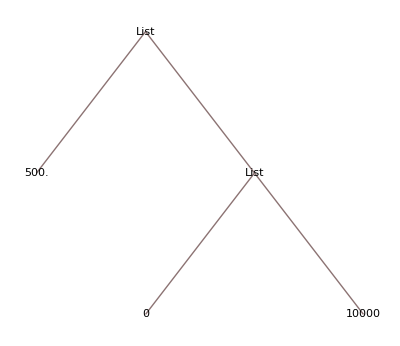

```mathematica
TreeForm[{0.10/2 10000,{0,10000}}]
```

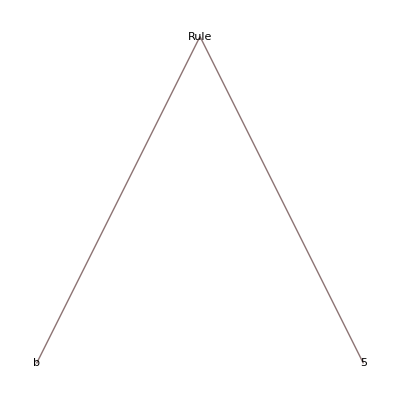

```mathematica
TreeForm[b->5]
```

```mathematica
Rule[b,5]
```

b→5

```mathematica
TimeValue[Annuity[{0.10/2 10000,{0,10000}},30,1/2],EffectiveInterest[0.06,1/2],0]
```

15535.1

#### Pricing after Issuance (two examples: relative time and actual date)

Price of a 10-year semiannual coupon bond with a coupon rate of 5.75% and a 5% yield 9 months after the issue date:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.0575,"Maturity"->10,"CouponInterval"->1/2},{"InterestRate"->.05,"Settlement"->9/12}]
```

1054.92

Price of a 4% coupon quarterly bond maturing December 31, 2030 and settling September 5, 2013 assuming the yield is at par:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.04,"Settlement"->{2013,9,5}}]
```

999.99

… assuming the yield is at 6%, and, hence, the bond is at discount:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.06,"Settlement"->{2013,9,5}}]
```

785.492

… assuming the yield is at 3%, and, hence, the bond is at premium:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.04,"Maturity"->{2030,12,31},"CouponInterval"->1/4},{"InterestRate"->.03,"Settlement"->{2013,9,5}}]
```

1134.68

#### Accrued Interest

Accrued interest for a semiannual bond maturing on December 31, 2030 and settling on November 12, 2010, using the "Actual/360" day count convention:

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.07,"Maturity"->{2030,12,31},"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->{2016,9,26},"DayCountBasis"->"Actual/360"},"AccruedInterest"]
```

17.1111

```mathematica
FinancialBond[{"FaceValue"->1000,"Coupon"->0.07,"Maturity"->{2030,12,31},"CouponInterval"->1/2},{"InterestRate"->0.06,"Settlement"->{2010,11,12},"DayCountBasis"->"30/360"},"AccruedInterest"]
```

25.6667

#### Yield Computation (using FindRoot[ ])

Implied yield to maturity for a quarterly coupon bond settling on January 6, 2018 and valued at $900:

```mathematica
AMSexample=y/.FindRoot[FinancialBond[{"Coupon"->0.05,"FaceValue"->1000,"Maturity"->{2018,1,6},"CouponInterval"->1/4},{"InterestRate"->y,"Settlement"->{2012,1,6}}]==900,{y,.05}]
```

0.070589

```mathematica
AMSexample
```

0.070589

```mathematica
z+x/.{x->3.14,z->45.1}
```

48.24

#### Yield versus Price Analysis (Using Table[ ], TableForm[ ], and ListLinePlot[ ])

```mathematica
mnYieldVsPrice=Table[
{
p,
y/.FindRoot[
FinancialBond[
{"FaceValue"->1000,"Coupon"->0.05,"Maturity"->{2018,6,31},"CouponInterval"->1/4},
{"InterestRate"->y,"Settlement"->{2012,1,6}}
]==p,
{y,0.05/2 1000}
]
},
{p,750,1250,50}
]
```

{{750,0.103374},{800,0.0911853},{850,0.0798533},{900,0.069269},{950,0.0593426},{1000,0.0499993},{1050,0.0411763},{1100,0.0328202},{1150,0.0248856},{1200,0.0173329},{1250,0.0101282}}

```mathematica
TableForm[mnYieldVsPrice,TableHeadings->{None,{"Price","Yield"}}]
```

Price | Yield
750 | 0.103374
800 | 0.0911853
850 | 0.0798533
900 | 0.069269
950 | 0.0593426
1000 | 0.0499993
1050 | 0.0411763
1100 | 0.0328202
1150 | 0.0248856
1200 | 0.0173329
1250 | 0.0101282

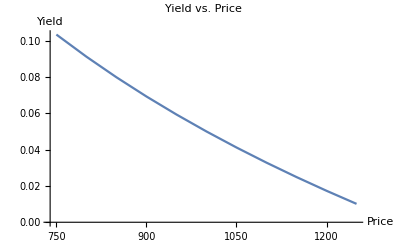

```mathematica
ListLinePlot[mnYieldVsPrice,AxesLabel->{"Price","Yield"},PlotLabel->Style["Yield vs. Price",FontSize->14]]
```